# Define functions for MAD data

### Extract the coordinates: BetaX

```mathematica
Clear[GetBetaX];
GetBetaX[x_]:=Module[
{f},
f[y_]:={y[[2]],y[[13]]};
f/@x
]
```

### Extract the coordinates: BetaY

```mathematica
Clear[GetBetaY];
GetBetaY[x_]:=Module[
{f},
f[y_]:={y[[2]],y[[14]]};
f/@x
]
```

### Extract the coordinates: X,Y

```mathematica
Clear[GetXY];
GetXY[x_]:=Module[
{f},
f[y_]:={y[[2]],y[[7]]};
f/@x
]
```

# Get TFS file. Output from: http://project-ps-optics.web.cern.ch/project-PS-optics/cps/TransLines/Linac2-PSB/2014/out/ltltbbi.sur

```mathematica
file2011=Import["http://project-ps-optics.web.cern.ch/project-PS-optics/cps/TransLines/Linac2-PSB/2014/cmdx/test_YASP/ltltbbi_optics_2011.out","Table"];
file2014=Import["http://project-ps-optics.web.cern.ch/project-PS-optics/cps/TransLines/Linac2-PSB/2014/cmdx/test_YASP/ltltbbi_optics_2014.out","Table"];
```

```mathematica
file2011[[Range[1,91]]]
```

{{@,NAME,%09s,PTC_TWISS},{@,TYPE,%05s,TWISS},{@,SEQUENCE,%07s,LTLTBBI},{@,PARTICLE,%06s,PROTON},{@,MASS,%le,0.93827},{@,CHARGE,%le,1.},{@,ENERGY,%le,0.98847},{@,PC,%le,0.311},{@,GAMMA,%le,1.0535},{@,KBUNCH,%le,1.},{@,BCURRENT,%le,0.},{@,SIGE,%le,0.001},{@,SIGT,%le,0.},{@,NPART,%le,0.},{@,EX,%le,0.00004},{@,EY,%le,0.00002},{@,ET,%le,1.},{@,DELTAP,%le,0.},{@,LENGTH,%le,131.205},{@,ALPHA_C,%le,-1.×10^6},{@,ALPHA_C_P,%le,-1.×10^6},{@,ALPHA_C_P2,%le,-1.×10^6},{@,ALPHA_C_P3,%le,-1.×10^6},{@,ETA_C,%le,-1.×10^6},{@,GAMMA_TR,%le,-1.×10^6},{@,Q1,%le,2.95208},{@,Q2,%le,2.47539},{@,DQ1,%le,-1.×10^6},{@,DQ2,%le,-1.×10^6},{@,QS,%le,-1.×10^6},{@,BETA_X_MIN,%le,0.71375},{@,BETA_X_MAX,%le,108.219},{@,BETA_Y_MIN,%le,0.24444},{@,BETA_Y_MAX,%le,647.081},{@,BETA11MIN,%le,0.71375},{@,BETA11MAX,%le,108.219},{@,BETA12MIN,%le,0.},{@,BETA12MAX,%le,0.},{@,BETA13MIN,%le,0.},{@,BETA13MAX,%le,0.},{@,BETA21MIN,%le,0.},{@,BETA21MAX,%le,0.},{@,BETA22MIN,%le,0.24444},{@,BETA22MAX,%le,647.081},{@,BETA23MIN,%le,0.},{@,BETA23MAX,%le,0.},{@,BETA31MIN,%le,0.},{@,BETA31MAX,%le,0.},{@,BETA32MIN,%le,0.},{@,BETA32MAX,%le,0.},{@,BETA33MIN,%le,0.},{@,BETA33MAX,%le,0.},{@,DISP1MIN,%le,-10.2778},{@,DISP1MAX,%le,5.66915},{@,DISP2MIN,%le,-1.18904},{@,DISP2MAX,%le,1.78678},{@,DISP3MIN,%le,0.},{@,DISP3MAX,%le,0.},{@,DISP4MIN,%le,0.},{@,DISP4MAX,%le,0.},{@,ORBIT_X,%le,0.},{@,ORBIT_PX,%le,0.},{@,ORBIT_Y,%le,0.},{@,ORBIT_PY,%le,0.},{@,ORBIT_PT,%le,0.},{@,ORBIT_-CT,%le,0.},{@,XCORMS,%le,0.00161},{@,PXCORMS,%le,0.00038},{@,YCORMS,%le,0.},{@,PYCORMS,%le,0.},{@,TCORMS,%le,0.},{@,PTCORMS,%le,0.},{@,XCOMIN,%le,-0.00559},{@,XCOMAX,%le,0.00359},{@,PXCOMIN,%le,-0.00101},{@,PXCOMAX,%le,0.00274},{@,YCOMIN,%le,0.},{@,YCOMAX,%le,0.},{@,PYCOMIN,%le,0.},{@,PYCOMAX,%le,0.},{@,TCOMIN,%le,0.},{@,TCOMAX,%le,0.},{@,PTCOMIN,%le,0.},{@,PTCOMAX,%le,0.},{@,TITLE,%56s,LT-LTB-BI 2011 optics. Protons - 311 MeV/c (Ekin=50 MeV)},{@,ORIGIN,%22s,MAD-X 5.02.00 Linux 64},{@,DATE,%08s,26/08/14},{@,TIME,%08s,17.07.28},{*,NAME,S,ANGLE,K1L,K2L,K3L,X,Y,PX,PY,ALFA11,ALFA22,BETA11,BETA22},{$,%s,%le,%le,%le,%le,%le,%le,%le,%le,%le,%le,%le,%le,%le},{LTLTBBI$START,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.19,0.103,1.342,2.48}}

```mathematica
Length[file2014]
```

345

```mathematica
file2014[[Range[91,110]]]
```

{{LTLTBBI$START,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.19,0.103,1.342,2.48},{LT$START,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.19,0.103,1.342,2.48},{BEGLT,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.19,0.103,1.342,2.48},{DRIFT_0,0.048,0.,0.,0.,0.,0.,0.,0.,0.,-0.22706,0.08344,1.36202,2.47105},{LT.VVS10,0.048,0.,0.,0.,0.,0.,0.,0.,0.,-0.22706,0.08344,1.36202,2.47105},{DRIFT_1,0.398,0.,0.,0.,0.,0.,0.,0.,0.,-0.49728,-0.05919,1.61554,2.46256},{LT.DHZ10,0.398,0.,0.,0.,0.,0.,0.,0.0005,0.,-0.49728,-0.05919,1.61554,2.46256},{LT.DVT10,0.398,0.,0.,0.,0.,0.,0.,0.0005,0.,-0.49728,-0.05919,1.61554,2.46256},{DRIFT_2,1.4,0.,0.,0.,0.,0.0005,0.,0.0005,0.,-1.27088,-0.46751,3.38723,2.99031},{LT.BPM10,1.4,0.,0.,0.,0.,0.0005,0.,0.0005,0.,-1.27088,-0.46751,3.38723,2.99031},{DRIFT_3,1.8495,0.,0.,0.,0.,0.00073,0.,0.0005,0.,-1.61792,-0.65068,4.68575,3.49293},{LT.QFN10,2.1045,0.,1.14136,0.,0.,0.00074,0.,-0.00036,0.,3.44432,-5.99947,4.16887,5.04134},{DRIFT_4,2.147,0.,0.,0.,0.,0.00073,0.,-0.00036,0.,3.31319,-6.31134,3.88167,5.56454},{LT.BEC1,2.147,0.,0.,0.,0.,0.00073,0.,-0.00036,0.,3.31319,-6.31134,3.88167,5.56454},{DRIFT_5,2.41,0.,0.,0.,0.,0.00063,0.,-0.00036,0.,2.50168,-8.24125,2.35236,9.39188},{LT.BCT10,2.41,0.,0.,0.,0.,0.00063,0.,-0.00036,0.,2.50168,-8.24125,2.35236,9.39188},{DRIFT_6,2.6495,0.,0.,0.,0.,0.00055,0.,-0.00036,0.,1.76268,-9.99872,1.33105,13.7604},{LT.QDN12,2.9045,0.,-0.87648,0.,0.,0.00052,0.,0.0001,0.,0.35327,2.88514,0.82838,15.7227},{DRIFT_7,3.089,0.,0.,0.,0.,0.00053,0.,0.0001,0.,0.10275,2.77572,0.74424,14.6783},{LT.BHZ10,3.595,0.,0.,0.,0.,0.00058,0.,0.0001,0.,-0.58431,2.47565,0.98791,12.0211}}

```mathematica
XY2011=GetXY[file2011[[Range[91,337]]]];
XY2014=GetXY[file2014[[Range[91,345]]]];
```

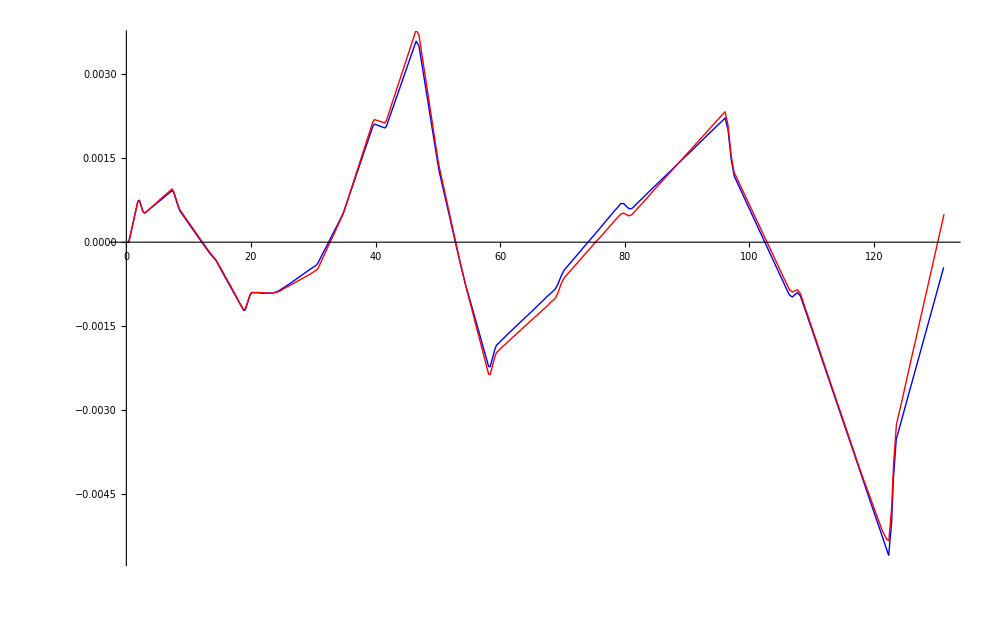

```mathematica
Plot2011=ListLinePlot[XY2011,PlotStyle->Blue];
Plot2014=ListLinePlot[XY2014,PlotStyle->Red];
Show[Plot2011,Plot2014,ImageSize->1000]
```

```mathematica
BetaX2011=GetBetaX[file2011[[Range[91,337]]]];
BetaX2014=GetBetaX[file2014[[Range[91,345]]]];
BetaY2011=GetBetaY[file2011[[Range[91,337]]]];
BetaY2014=GetBetaY[file2014[[Range[91,345]]]];
```

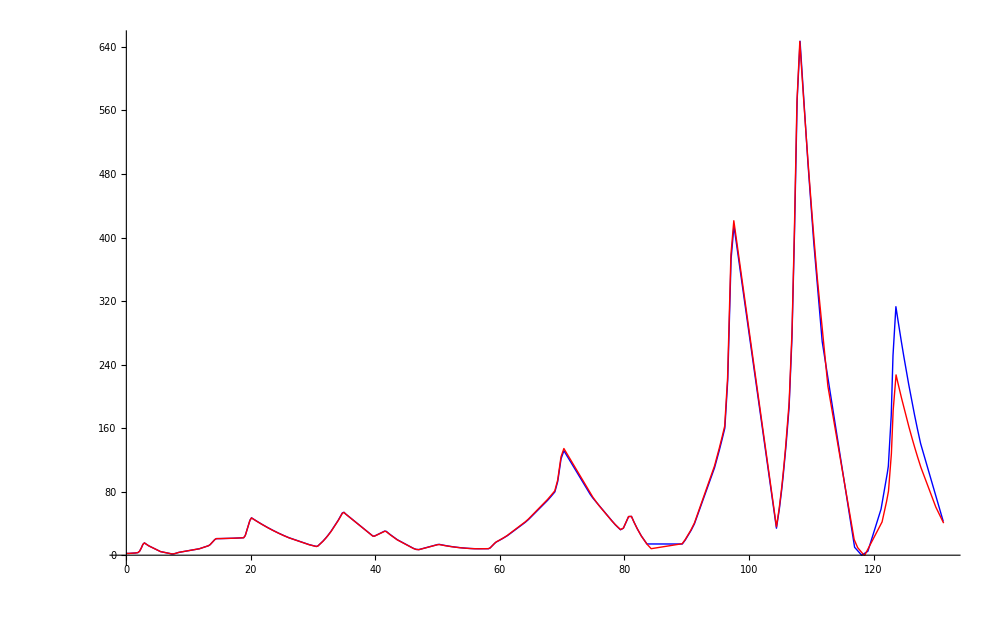

```mathematica
Plot2011BetaY=ListLinePlot[BetaY2011,PlotStyle->Blue,PlotRange->All];
Plot2014BetaY=ListLinePlot[BetaY2014,PlotStyle->Red,PlotRange->All];
Show[Plot2011BetaY,Plot2014BetaY,ImageSize->1000]
```

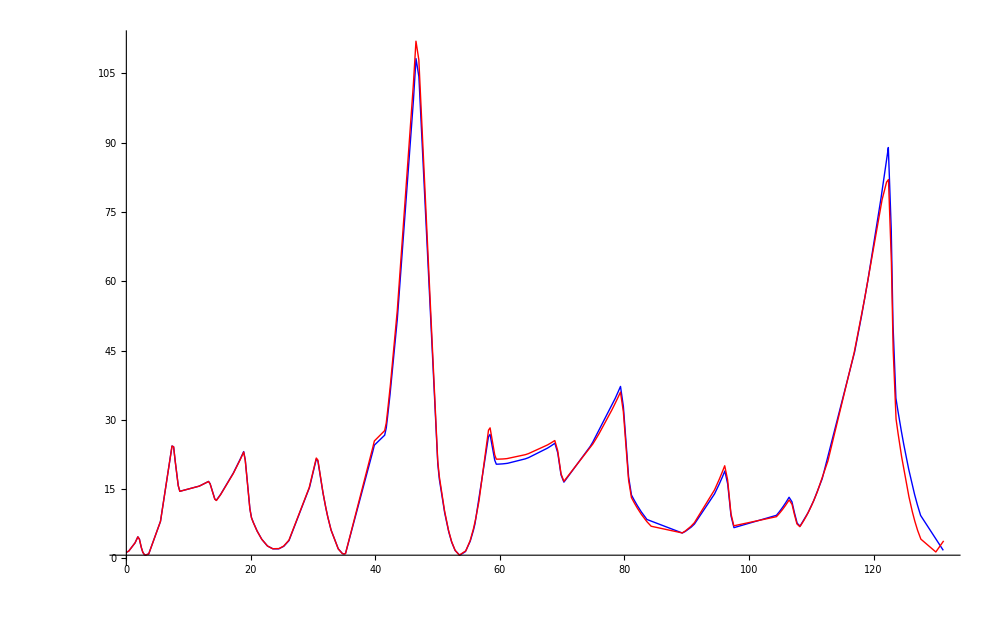

```mathematica
Plot2011BetaX=ListLinePlot[BetaX2011,PlotStyle->Blue,PlotRange->All];
Plot2014BetaX=ListLinePlot[BetaX2014,PlotStyle->Red,PlotRange->All];
Show[Plot2011BetaX,Plot2014BetaX,ImageSize->1000]
```